```mathematica
(*Mathematica*)
```

```mathematica
{Z0,Z1,Z2,Z3}={0,1,x+I*y,z+t}
```

{0,1,x+ⅈ y,t+z}

```mathematica
{Z0b,Z1b,Z2b,Z3b}={1,0,x-I*y,-z+t}
```

{1,0,x-ⅈ y,t-z}

```mathematica
IdentityMatrix[4]
```

{{1,0,0,0},{0,1,0,0},{0,0,1,0},{0,0,0,1}}

```mathematica
m4={{1,0,z-t,-x-I*y},
{0,1,-x+I*y,z+t},
{0,0,1,0},
{0,0,0,1}}
```

{{1,0,-t+z,-x-ⅈ y},{0,1,-x+ⅈ y,t+z},{0,0,1,0},{0,0,0,1}}

```mathematica
u=ExpandAll[m4.{Z0,Z1,Z2,Z3}]
```

{-2 t x-2 ⅈ t y,1+t^2-x^2-y^2+2 t z+z^2,x+ⅈ y,t+z}

```mathematica
v=ExpandAll[m4.{Z0b,Z1b,Z2b,Z3b}]
```

{1-2 t x+2 x z,t^2-x^2+2 ⅈ x y+y^2-z^2,x-ⅈ y,t-z}

```mathematica
w=Join[Table[u[[i]]==0,{i,2}],Table[v[[i]]==0,{i,2}]]
```

{-2 t x-2 ⅈ t y==0,1+t^2-x^2-y^2+2 t z+z^2==0,1-2 t x+2 x z==0,t^2-x^2+2 ⅈ x y+y^2-z^2==0}

```mathematica
s={x,y,z,t}/.NSolve[w,{x,y,z,t}]
```

{{-0.433013-0.25 ⅈ,0.25-0.433013 ⅈ,0.433013-0.75 ⅈ,-0.433013-0.25 ⅈ},{0.433013+0.25 ⅈ,-0.25+0.433013 ⅈ,-0.433013+0.75 ⅈ,0.433013+0.25 ⅈ},{0.+0.5 ⅈ,-0.5,0.,0.-1. ⅈ},{0.-0.5 ⅈ,0.5,0.,0.+1. ⅈ},{0.433013-0.25 ⅈ,0.25+0.433013 ⅈ,-0.433013-0.75 ⅈ,0.433013-0.25 ⅈ},{-0.433013+0.25 ⅈ,-0.25-0.433013 ⅈ,0.433013+0.75 ⅈ,-0.433013+0.25 ⅈ}}

```mathematica
Length[s]
```

6

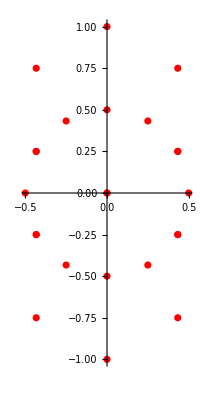

```mathematica
Show[Table[ComplexListPlot[s[[i]],PlotStyle->Red],{i,Length[s]}],PlotRange->All]
```

```mathematica
(* solutions as Killing vectors in a Cartan matrix*)
```

```mathematica
ca=Table[2*s[[i]].s[[j]]/(s[[i]].s[[i]]),{i,6},{j,6}]//Chop
```

{{2.,-2.,-1.-1.73205 ⅈ,1.+1.73205 ⅈ,2.-3.4641 ⅈ,-2.+3.4641 ⅈ},{-2.,2.,1.+1.73205 ⅈ,-1.-1.73205 ⅈ,-2.+3.4641 ⅈ,2.-3.4641 ⅈ},{0.5-0.866025 ⅈ,-0.5+0.866025 ⅈ,2.,-2.,0.5+0.866025 ⅈ,-0.5-0.866025 ⅈ},{-0.5+0.866025 ⅈ,0.5-0.866025 ⅈ,-2.,2.,-0.5-0.866025 ⅈ,0.5+0.866025 ⅈ},{2.+3.4641 ⅈ,-2.-3.4641 ⅈ,-1.+1.73205 ⅈ,1.-1.73205 ⅈ,2.,-2.},{-2.-3.4641 ⅈ,2.+3.4641 ⅈ,1.-1.73205 ⅈ,-1.+1.73205 ⅈ,-2.,2.}}

```mathematica
Grid[ca]
```

2. | -2. | -1.-1.73205 ⅈ | 1.+1.73205 ⅈ | 2.-3.4641 ⅈ | -2.+3.4641 ⅈ
-2. | 2. | 1.+1.73205 ⅈ | -1.-1.73205 ⅈ | -2.+3.4641 ⅈ | 2.-3.4641 ⅈ
0.5-0.866025 ⅈ | -0.5+0.866025 ⅈ | 2. | -2. | 0.5+0.866025 ⅈ | -0.5-0.866025 ⅈ
-0.5+0.866025 ⅈ | 0.5-0.866025 ⅈ | -2. | 2. | -0.5-0.866025 ⅈ | 0.5+0.866025 ⅈ
2.+3.4641 ⅈ | -2.-3.4641 ⅈ | -1.+1.73205 ⅈ | 1.-1.73205 ⅈ | 2. | -2.
-2.-3.4641 ⅈ | 2.+3.4641 ⅈ | 1.-1.73205 ⅈ | -1.+1.73205 ⅈ | -2. | 2.

```mathematica
Eigenvalues[ca]//Chop
```

{12.,-2.02624×10^-8-2.67609×10^-8 ⅈ,2.02624×10^-8+2.67609×10^-8 ⅈ,0,0,0}

```mathematica
WeightedAdjacencyGraph[ca]
```

-Graphics-

```mathematica
(*end*)
```